First these are the necessary functions to define the exact amplitude.

```mathematica
FId[x_]:=-2(Log[1+x]+Log[Gamma[1/2+ⅈ Log[x]/(2π)]])
Aexact[n_,m_]:= 2 Sqrt[n*m] SeriesCoefficient[FId[ⅇ^x(1+s)/(1-s)(1-t)/(1+t)],{s,0,2n},{t,0,2m}];
```

The matrix elements of the constraint operator.  (p^2-Θ/(12π G)) where is not the original scalar field momentum but is rescaled by 12π G appropriately

```mathematica
OffD[n_,m_]:= Sqrt[n*m](n+m)/2;
Diag[n_]:=p^2-2 n^2
```

These are the functions generating the amplitudes.  Nume, Denom , and Amp together defines the amplitude for each path.  Changes and Paths together define the space of paths given a set number of transitions.  Finally ManyAmp generates the overall amplitude for the full set of paths with a fixed number of transitions

```mathematica
Nume[v_]:=(ⅈ (-1)^(Length[v]-1))/(2π)Product[OffD[v[[i]],v[[i+1]]],{i,1,Length[v]-1}];
Denom[v_]:=Product[(Diag[v[[i]]]),{i,1,Length[v]}];
Amp[v_]:=Nume[v](1/Denom[v]);
Changes[m_,vi_,vf_]:=(
diff=(vf-vi);
base=Join[Table[1,{i,1,m/2+diff/2}],Table[-1,{i,1,m/2-diff/2}]];
changes=Permutations[base];
numpaths=Length[changes];)
Paths[m_,vi_,vf_]:=(
paths=Table[1,{j,1,numpaths}];
path=Table[vi,{i,1,m+1}];
For[j=1,j≤numpaths,j++,
For[i=1,i≤m,i++,
path[[i+1]]=path[[i]]+changes[[j]][[i]];];
paths[[j]]=path;
];);
NullPath[v_]:=Product[v[[i]],{i,1,Length[v]}];
ManyAmp[m_,vi_,vf_]:=(
Changes[m,vi,vf];
Paths[m,vi,vf];
Many=0;
For[i=1,i≤Length[paths],i++,
If[NullPath[paths[[i]]]==0,Many=Many,Many=Many+Amp[paths[[i]]]];
];
Many)
```

Finally we define a method to carry out the integral over the scalar field momentum using the residue theorem.  Important question -- is it more efficient to calculate residues for each history or compute the residue for the entire thing in the end ... seems like it does a perfectly good job.

```mathematica
Res[f_]:=(
func=Simplify[f];
poly = Denominator[func];
roots = p/.Solve[poly==0,p];
roots = Abs[roots];
roots =Table[Split[Sort[roots]][[i]][[1]],{i,1,Length[Split[Sort[roots]]]}];
res=0;
For[i=1,i<=Length[roots],i++,
res=res+2π ⅈ Residue[func,{p,roots[[i]]}];];
res)
```

```mathematica
Amp0=Res[-ManyAmp[0,1,1] ⅇ^(ⅈ p x) 2 p ];
Amp2 =Res[-ManyAmp[2,1,1] ⅇ^(ⅈ p x)2p];
Amp4 = Res[-ManyAmp[4,1,1] ⅇ^(ⅈ p x)2p];
Amp6= Res[-ManyAmp[6,1,1] ⅇ^(ⅈ p x)2p];
Amp8 = Res[-ManyAmp[8,1,1] ⅇ^(ⅈ p x)2p];
Amp10= Res[-ManyAmp[10,1,1] ⅇ^(ⅈ p x)2p];
Amp12 = Res[-ManyAmp[12,1,1] ⅇ^(ⅈ p x)2p];
```

```mathematica
Amp14 = Expand[Res[-ManyAmp[14,1,1] ⅇ^(ⅈ p x)2p]];
```

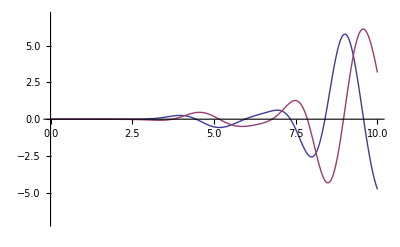

```mathematica
Plot[{Re[Amp14],Im[Amp14]},{x,0,10},PlotRange->{-7,7}]
```

```mathematica
Amp16 = Expand[Res[-ManyAmp[16,1,1] ⅇ^(ⅈ p x)2p]];
```

```mathematica
Amp18 = Expand[Res[-ManyAmp[18,1,1] ⅇ^(ⅈ p x)2p]];
```

```mathematica
aex = Aexact[1,1];
```

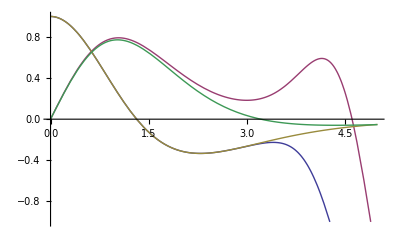

```mathematica
Plot[{Re[Amp0+Amp2+Amp4+Amp6+Amp8+Amp10+Amp12 + Amp16+Amp14+Amp18],Im[Amp0+Amp2+Amp4+Amp6+Amp8+Amp10+Amp12 + Amp16+Amp14+Amp18],Re[aex],Im[aex]},{x,0,5},PlotRange->{-1,1}]
```

```mathematica
AmpLarge0=Res[-ManyAmp[9,1,10] ⅇ^(ⅈ p x) 2 p ]
```

(4199 √(5/2) ⅇ^(ⅈ √2 x))/16777216-(12597 √(5/2) ⅇ^(2 ⅈ √2 x))/16777216+(8721 √(5/2) ⅇ^(3 ⅈ √2 x))/8388608-(969 √(5/2) ⅇ^(4 ⅈ √2 x))/1048576+(4845 √(5/2) ⅇ^(5 ⅈ √2 x))/8388608-(8721 √(5/2) ⅇ^(6 ⅈ √2 x))/33554432+(2793 √(5/2) ⅇ^(7 ⅈ √2 x))/33554432-(19 √(5/2) ⅇ^(8 ⅈ √2 x))/1048576+(81 √(5/2) ⅇ^(9 ⅈ √2 x))/33554432-(5 √(5/2) ⅇ^(10 ⅈ √2 x))/33554432

```mathematica
aexLarge = Simplify[Aexact[1,10]];
```

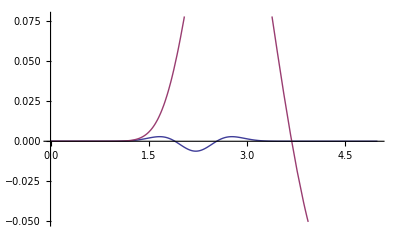

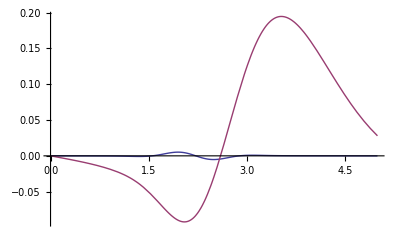

```mathematica
Plot[{Re[AmpLarge0],Re[aexLarge]},{x,0,5}]
Plot[{Im[AmpLarge0],Im[aexLarge]},{x,0,5}]
```